```mathematica
Vf[]:={{Module[{},
ClearAll[x,y,H1,H2,U1,U2];
a=1;
b=2;
c=1;
h=5;
F1[v1_,v2_,v3_]=v3*((v2)^h/(1+(v2)^h))-a*v1;
F2[v1_,v2_,v3_]=b*v1-c*v2;

Q1[s_,v1_,v2_]=8; 
Q2[s_,v1_,v2_]=v2; (*To są funckje przełączenia*)
Subscript[a, 0]=0;
Subscript[a, 1]=1; (*Wartości przyjmowane przez proces losowy*)
Subscript[x, 0]=1;
Subscript[y, 0]=1.5;
Subscript[t, 0]=0; (*Początkowy czas*)
 (*Wartości przełączeń, można wywalić jak zmieni się funckje Q1, Q2*)
Do[
{Clear[s],
Subscript[t, i]=Subscript[t, i-1]+RandomReal[ExponentialDistribution[Q1[Subscript[t, i-1],Subscript[x, Subscript[t, i-1]],Subscript[y, Subscript[t, i-1]]]]];
s=NDSolve[{x'[t]==F1[x[t],y[t],Subscript[a, 0]],y'[t]==F2[x[t],y[t],Subscript[a, 0]],

x[Subscript[t, i-1]]==Subscript[x, 0],y[Subscript[t, i-1]]==Subscript[y, 0]},{x,y},{t,Subscript[t, i-1],Subscript[t, i]+2}];
(*Print[Subscript[z, Subscript[t, i-1]]],
Print[Q1[Subscript[t, i-1],Subscript[x, Subscript[t, i-1]],Subscript[y, Subscript[t, i-1]],Subscript[z, Subscript[t, i-1]]]],*)
Subscript[x, 0]=x[Subscript[t, i]]/.s; Subscript[y, 0]=y[Subscript[t, i]]/.s;
Subscript[x, 0]=First[Flatten[Subscript[x, 0]]]; Subscript[y, 0]=First[Flatten[Subscript[y, 0]]];


Subscript[y, Subscript[t, i]]=First[Flatten[y[Subscript[t, i]]/.s]];
Subscript[x, Subscript[t, i]]=First[Flatten[x[Subscript[t, i]]/.s]];
Clear[w],
Subscript[t, i+1]=Subscript[t, i]+RandomReal[ExponentialDistribution[Q2[Subscript[t, i],Subscript[x, Subscript[t, i]],Subscript[y, Subscript[t, i]]]]];
w=NDSolve[{x'[t]==F1[x[t],y[t],Subscript[a, 1]],y'[t]==F2[x[t],y[t],Subscript[a, 1]],x[Subscript[t, i]]==Subscript[x, 0],y[Subscript[t, i]]==Subscript[y, 0]},{x,y},{t,Subscript[t, i],Subscript[t, i+1]+2}];
Subscript[x, 0]=x[Subscript[t, i+1]]/.w;Subscript[y, 0]=y[Subscript[t, i+1]]/.w;
Subscript[x, 0]=First[Flatten[Subscript[x, 0]]]; Subscript[y, 0]=First[Flatten[Subscript[y, 0]]];

Subscript[y, Subscript[t, i+1]]=First[Flatten[y[Subscript[t, i+1]]/.s]];
Subscript[x, Subscript[t, i+1]]=First[Flatten[x[Subscript[t, i+1]]/.s]];
Subscript[u1, i-1][t_]=Piecewise[({{x[t]/.s, Subscript[t, i-1]<=t<Subscript[t, i]}, {x[t]/.w, Subscript[t, i]<=t<Subscript[t, i+1]}})];
Subscript[u2, i-1][t_]=Piecewise[({{y[t]/.s, Subscript[t, i-1]<=t<Subscript[t, i]}, {y[t]/.w, Subscript[t, i]<=t<Subscript[t, i+1]}})];

U1[t_]=Piecewise[({{U1[t], Subscript[t, 0]<=t<Subscript[t, i-1]}, {Subscript[u1, i-1][t], Subscript[t, i-1]<=t<Subscript[t, i+1]}})];
U2[t_]=Piecewise[({{U2[t], Subscript[t, 0]<=t<Subscript[t, i-1]}, {Subscript[u2, i-1][t], Subscript[t, i-1]<=t<Subscript[t, i+1]}})];

If[Subscript[t, i+1]>150, Break[] ]},{i,1,1300,2}];
]}, {□}}
```

```mathematica
|
```

```mathematica
Vf[] (*Turaj realizujemy funckje Vf i rysujemy realizacjie procesu*)
(*Plot[U1[t],{t,0,140},PlotRange->({{0, 140}, {0, 2.1}}),AxesLabel->{t,Subscript[x, 1][t]}]
Plot[U2[t],{t,0,140},PlotRange->({{0, 140}, {0, 2.1}}),AxesLabel->{t,Subscript[x, 2][t]}]*)


(*Rysujemy ładnie wykres realizacji po współrzędnych procesu PDMP*)

ParametricPlot[{First[Flatten[U1[t]]],First[Flatten[U2[t]]]},{t,0,340},PlotRange->({{0, 2.1}, {0, 2.1}}),AxesLabel->{Style["x",30],Style["y",30]}, TicksStyle->{{FontSize->28},{FontSize->28}}, PlotStyle->Gray, ImageSize->Large]
```

InterpolatingFunction::dmval: Input value {9.23604} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.1612} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

RandomReal::posprm: Parameter -7.90464×10^-11 at position 1 in ExponentialDistribution[-7.90464×10^-11] is expected to be positive.

NDSolve::ndnl: Endpoint 37.9199+RandomReal[ExponentialDistribution[-7.90464×10^-11]] in {t,35.9199,37.9199+RandomReal[ExponentialDistribution[-7.90464×10^-11]]} is not a real number.

ReplaceAll::reps: {NDSolve[{x'[t]==-x[t]+y[«1»]^5/Plus[«2»],y'[t]==2 x[t]-y[t],x[35.9199]==-1.71608×10^-12,y[35.9199]==-7.90464×10^-11},{x,y},{t,35.9199,37.9199+RandomReal[ExponentialDistribution[-7.90464×10^-11]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnl: Endpoint 37.9199+RandomReal[ExponentialDistribution[-7.90464×10^-11]] in {t,35.9199,37.9199+RandomReal[ExponentialDistribution[-7.90464×10^-11]]} is not a real number.

General::stop: Further output of NDSolve::ndnl will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {x'[t]==-x[t],y'[t]==2 x[t]-y[t],True,True}.

RandomReal::posprm: Parameter y[35.9635+RandomReal[ExponentialDistribution[-7.90464×10^-11]]] at position 1 in ExponentialDistribution[y[35.9635+RandomReal[ExponentialDistribution[-7.90464×10^-11]]]] is expected to be positive.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {x'[t]==-x[t]+y[t]^5/(1+y[«1»]^5),y'[t]==2 x[t]-y[t],True,True}.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {x'[t]==-x[t],y'[t]==2 x[t]-y[t],True,True}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

RandomReal::posprm: Parameter y[36.065+RandomReal[ExponentialDistribution[-7.90464×10^-11]]+RandomReal[ExponentialDistribution[y[35.9635+RandomReal[ExponentialDistribution[«1»]]]]]] at position 1 in ExponentialDistribution[y[36.065+RandomReal[ExponentialDistribution[-7.90464×10^-11]]+RandomReal[ExponentialDistribution[y[35.9635+RandomReal[«1»]]]]]] is expected to be positive.

General::stop: Further output of RandomReal::posprm will be suppressed during this calculation.

$Aborted

NDSolve::dsvar: 0.00693878 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00693878]==-x[0.00693878],y'[0.00693878]==2 x[0.00693878]-y[0.00693878],True,True},{x,y},{0.00693878,35.9199+RandomReal[ExponentialDistribution[-7.90464×10^-11]],37.9635+RandomReal[ExponentialDistribution[-7.90464×10^-11]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00693878 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00693878]==-x[0.00693878]+y[«1»]^5/Plus[«2»],y'[0.00693878]==2 x[0.00693878]-y[0.00693878],True,True},{x,y},{0.00693878,35.9635+RandomReal[ExponentialDistribution[-7.90464×10^-11]],37.9635+RandomReal[ExponentialDistribution[-7.90464×10^-11]]+RandomReal[ExponentialDistribution[y[Plus[«2»]]]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00693878 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.00693878]==-x[0.00693878],y'[0.00693878]==2 x[0.00693878]-y[0.00693878],True,True},{x,y},{0.00693878,35.9635+RandomReal[ExponentialDistribution[-7.90464×10^-11]]+RandomReal[ExponentialDistribution[y[Plus[«2»]]]],38.065+RandomReal[ExponentialDistribution[-7.90464×10^-11]]+RandomReal[ExponentialDistribution[y[Plus[«2»]]]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

```mathematica
(*p=400; (*To jest ilość realizacji jakie zrobimy, im większa tym dokładniejsze będą wykresy*)
Monitor[n=0; Do[{ClearAll[x,y, z1,z2,f1,U1,U2,K1,u1,u2],
Vf[];Do[{
Subscript[b1, l][m]=U1[m];
Subscript[b2, l][m]=U2[m];
},{m,1,140,0.05}];
n=(l*100)/p},{l,p}];n,Row[{ProgressIndicator[Dynamic[n],{0,100}],Row[{n,"%"}]}]] (*Dodatkowy funkcja paska postępu, bo zajmuje to trochę, czasem nawet koło 2h*)
Do[{
Subscript[z1, m]=Flatten[Table[Subscript[b1, l][m],{l,p}]];
Subscript[z2, m]=Flatten[Table[Subscript[b2, l][m],{l,p}]];

Subscript[f1, m]=Partition[Riffle[Subscript[z1, m],Subscript[z2, m]],2];

},{m,1,140,0.05}]
Histogram[Flatten[Table[Subscript[z1, m],{m,1,140,0.05}],1],AxesLabel->{"",Subscript[x, 1]}];
Histogram[Flatten[Table[Subscript[z2, m],{m,1,140,0.05}],1],AxesLabel->{"",Subscript[x, 2]}];
(*To są częstości dla procesu (x,y,z) na całym przedziale czasu, taka całka nietylko po zmiennych ale jeszcze po czasie.*)
K1=Flatten[Table[Subscript[f1, m],{m,1,140,0.05}],1];

SmoothHistogram3D[K1,AxesLabel->{Subscript[x, 1],Subscript[x, 2]}] *)
```

InterpolatingFunction::dmval: Input value {3.71713} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Set::write: Tag List in {0.417367}[1.] is Protected.

Set::write: Tag List in {0.610726}[1.] is Protected.

Set::write: Tag List in {0.707098}[1.] is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

100

SmoothHistogram3D::ldata: {{{0.417367}[1.], {0.610726}[1.]}, {{0.936604}[1.], {0.878224}[1.]}, {{0.417367}[1.05], {0.610726}[1.05]}, {{0.936604}[1.05], {0.878224}[1.05]}, {{0.417367}[1.1], {0.610726}[1.1]}, « 42 », {{0.936604}[2.15], {0.878224}[2.15]}, {{0.417367}[2.2], {0.610726}[2.2]}, {{0.936604}[2.2], {0.878224}[2.2]}, « 5512 »} is not a valid dataset or list of datasets.

SmoothHistogram3D::ldata: {{{0.417367}[1.], {0.707098}[1.]}, {{0.936604}[1.], {0.824492}[1.]}, {{0.417367}[1.05], {0.707098}[1.05]}, {{0.936604}[1.05], {0.824492}[1.05]}, {{0.417367}[1.1], {0.707098}[1.1]}, « 42 », {{0.936604}[2.15], {0.824492}[2.15]}, {{0.417367}[2.2], {0.707098}[2.2]}, {{0.936604}[2.2], {0.824492}[2.2]}, « 5512 »} is not a valid dataset or list of datasets.

SmoothHistogram3D::ldata: {{{0.610726}[1.], {0.707098}[1.]}, {{0.878224}[1.], {0.824492}[1.]}, {{0.610726}[1.05], {0.707098}[1.05]}, {{0.878224}[1.05], {0.824492}[1.05]}, {{0.610726}[1.1], {0.707098}[1.1]}, « 42 », {{0.878224}[2.15], {0.824492}[2.15]}, {{0.610726}[2.2], {0.707098}[2.2]}, {{0.878224}[2.2], {0.824492}[2.2]}, « 5512 »} is not a valid dataset or list of datasets.

SmoothHistogram3D::ldata: {{{0.417367}[1.], {0.758543}[1.]}, {{0.936604}[1.], {0.775068}[1.]}, {{0.417367}[1.05], {0.758543}[1.05]}, {{0.936604}[1.05], {0.775068}[1.05]}, {{0.417367}[1.1], {0.758543}[1.1]}, « 42 », {{0.936604}[2.15], {0.775068}[2.15]}, {{0.417367}[2.2], {0.758543}[2.2]}, {{0.936604}[2.2], {0.775068}[2.2]}, « 5512 »} is not a valid dataset or list of datasets.

SmoothHistogram3D::ldata: {{{0.610726}[1.], {0.758543}[1.]}, {{0.878224}[1.], {0.775068}[1.]}, {{0.610726}[1.05], {0.758543}[1.05]}, {{0.878224}[1.05], {0.775068}[1.05]}, {{0.610726}[1.1], {0.758543}[1.1]}, « 42 », {{0.878224}[2.15], {0.775068}[2.15]}, {{0.610726}[2.2], {0.758543}[2.2]}, {{0.878224}[2.2], {0.775068}[2.2]}, « 5512 »} is not a valid dataset or list of datasets.

SmoothHistogram3D::ldata: {{{0.707098}[1.], {0.758543}[1.]}, {{0.824492}[1.], {0.775068}[1.]}, {{0.707098}[1.05], {0.758543}[1.05]}, {{0.824492}[1.05], {0.775068}[1.05]}, {{0.707098}[1.1], {0.758543}[1.1]}, « 42 », {{0.824492}[2.15], {0.775068}[2.15]}, {{0.707098}[2.2], {0.758543}[2.2]}, {{0.824492}[2.2], {0.775068}[2.2]}, « 5512 »} is not a valid dataset or list of datasets.

```mathematica
p=300;
Monitor[n=0; Do[{ClearAll[x,y,z1,z2,f1,U1,U2,K1,u1,u2],
Vf[];
Subscript[b1, l]=U1[340];
Subscript[b2, l]=U2[340];

n=(l*100)/p},{l,p}];n,Row[{ProgressIndicator[Dynamic[n],{0,100}],Row[{n,"%"}]}]]
z1=Flatten[Table[Subscript[b1, l],{l,p}]];
z2=Flatten[Table[Subscript[b2, l],{l,p}]];

f1=Partition[Riffle[z1,z2],2];

(*Show[Histogram[z1,20,"PDF"],SmoothHistogram[z1],AxesLabel->{"",Subscript[x, 1]}]
Show[Histogram[z2,20,"PDF"],SmoothHistogram[z2],AxesLabel->{"",Subscript[x, 2]}]*)
(*Tutaj mamy częstości i przybiżone funckji gęstości dla poszczególnych zmiennych*)
SmoothHistogram3D[f1,PlotTheme->"Scientific",ImageSize->Large,TicksStyle->Directive[28],AxesLabel->{Style["x",32],Style["y",32]},PlotStyle->GrayLevel[0.5]]

(*Przybliżone funkcje gęstości dla każdych dwóch zmiennych*) 
(*SmoothDensityHistogram[f1,ColorFunction->Hue,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}]*)
```

InterpolatingFunction::dmval: Input value {32.0227} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {53.0519} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: (2.14479×10^-62)^5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.94676×10^-62)^5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

100

-Graphics3D-

InterpolatingFunction::dmval: Input value {2.90514} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {14.2105} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

RandomReal::posprm: Parameter -7.92198×10^-12 at position 1 in ExponentialDistribution[-7.92198×10^-12] is expected to be positive.

NDSolve::ndnl: Endpoint 64.8453+RandomReal[ExponentialDistribution[-7.92198×10^-12]] in {t,62.8453,64.8453+RandomReal[ExponentialDistribution[-7.92198×10^-12]]} is not a real number.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnl: Endpoint 64.8453+RandomReal[ExponentialDistribution[-7.92198×10^-12]] in {t,62.8453,64.8453+RandomReal[ExponentialDistribution[-7.92198×10^-12]]} is not a real number.

General::stop: Further output of NDSolve::ndnl will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {x'[t]==-x[t],y'[t]==2 x[t]-y[t],True,True}.

RandomReal::posprm: Parameter y[62.9893+RandomReal[ExponentialDistribution[-7.92198×10^-12]]] at position 1 in ExponentialDistribution[y[62.9893+RandomReal[ExponentialDistribution[-7.92198×10^-12]]]] is expected to be positive.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {x'[t]==-x[t]+y[t]^5/(1+y[«1»]^5),y'[t]==2 x[t]-y[t],True,True}.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {x'[t]==-x[t],y'[t]==2 x[t]-y[t],True,True}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

RandomReal::posprm: Parameter y[63.0124+RandomReal[ExponentialDistribution[-7.92198×10^-12]]+RandomReal[ExponentialDistribution[y[62.9893+RandomReal[ExponentialDistribution[«1»]]]]]] at position 1 in ExponentialDistribution[y[63.0124+RandomReal[ExponentialDistribution[-7.92198×10^-12]]+RandomReal[ExponentialDistribution[y[62.9893+RandomReal[«1»]]]]]] is expected to be positive.

General::stop: Further output of RandomReal::posprm will be suppressed during this calculation.

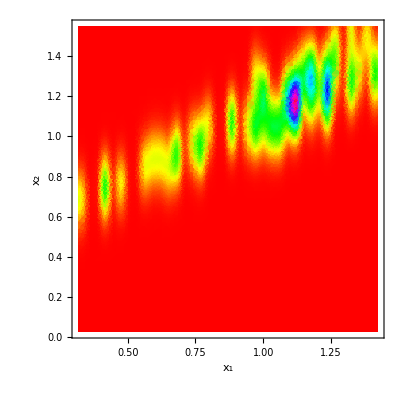

InterpolatingFunction::dmval: Input value {74.6652} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {82.8641} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
SmoothHistogram3D[f1,PlotStyle->Directive[RGBColor[0.5,0.5,0.5],Opacity[0.6880000000000001]],PlotTheme->"Scientific",ImageSize->Large,TicksStyle->Directive[28],AxesLabel->{Style["x",32],Style["y",32]}, PlotRange->{{0,1},{0,1},{0,1}}]
```